### Hamiltonian diagonalization

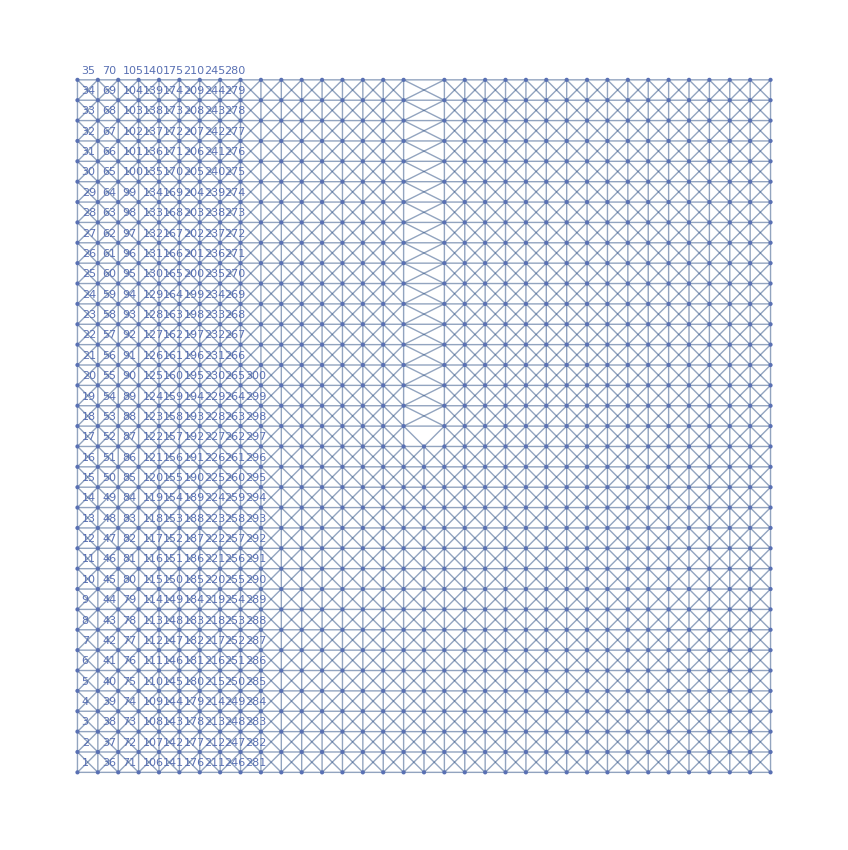

248

```mathematica
ClearAll["Global`*"];

(* parameters *)
n=35;(* side length of the open disc, can only be odd *)
nirreg=0;(* 0 mod 1 represent o=alpha, 1/2 mod 1 represent o=beta*)
δ=0.061;(* chemical potential increment*)
leftpt=0; (* magnetic field lower bond *)
rightpt=1; (* magnetic field upper bond *)
steps=7; (* magnetic field increment *)
mulow=-4;(* chemical potential lower bond *)
muup=4;(* chemical potential upper bond *)
t=0; (*diagonal link hopping strentgh, reduce to square lattice when t=0,*)

add=numofflux*2Pi/((n)^2);(* \phi *)
extra = add*nirreg; (* add extra flux to the irregular unit cell such that \phi_irreg = n_irreg*\phi *)

dist=Floor[(n)/2]-1;
(*initialize a clean lattice*)
g=GridGraph[{n,n},VertexLabels->Automatic];
emb=GraphEmbedding[g];

zeros=Table[0,{i,n^2},{j,n^2}];

adjxydiag1=Flatten[Table[({1+i+n*j,1+i+n*(j-1)+1})->1,{i,0,n-2},{j,1,n-1}]];
adjxydiag2=Flatten[Table[({1+i+n*j,1+i+n*(j+1)+1})->1,{i,0,n-2},{j,0,n-2}]];
diag=ReplacePart[zeros,adjxydiag1];
diag=ReplacePart[diag,adjxydiag2];
diag+=Transpose[diag];

adj=AdjacencyMatrix[g];
adj+=diag;
gg=AdjacencyGraph[adj,VertexCoordinates->emb,VertexLabels->Automatic];


(*add dislocation*)
centerPos=1+(n-1)*(n+1)/2;
Table[{centerPos+i,centerPos-n+i},{i,0,dist+1}];
gg=SimpleGraph[VertexContract[gg,Table[{centerPos+i,centerPos-n+i},{i,0,dist+1}]]];
gg=EdgeDelete[gg,centerPos-n<->centerPos+n-1];
Graph[gg,GraphLayout->"SpringEmbedding"]
(*gg=EdgeDelete[gg,{centerPos-n<->centerPos+n-1,centerPos-n<->centerPos-1,centerPos+n<->centerPos-1}]*)
emb=GraphEmbedding[gg];
adj=AdjacencyMatrix[gg];
zeros=Table[0,{i,Length[adj]},{j,Length[adj]}];
ones=Table[1,{i,Length[adj]},{j,Length[adj]}];
indexT= Table[VertexList[gg][[i]]->i,{i,1,Length[VertexList[gg]]}];


edge=Table[{EdgeList[gg][[i,1]],EdgeList[gg][[i,2]]},{i,Length[EdgeList[gg]]}];
(*
pathfull=Table[i+n*j<->i+n-1+n*j,{i,2,n},{j,0,n-2}]
pathlist=Table[centerPos-n+i+1<->centerPos+n+i,{i,0,dist}];
Do[pathfull[[i-1-Length[pathlist]]]=Append[pathfull[[i-1-Length[pathlist]]],pathlist[[i]]],{i,Length[pathlist]}];
pathfull;
HighlightGraph[gg,pathfull]

pathfull2=Table[i+n*j<->i+n+1+n*j,{i,1,n-1},{j,0,n-2}]
pathlist2=Table[centerPos-n+i<->centerPos+n+i+1,{i,0,dist}]
Do[pathfull2[[i-1-Length[pathlist2]]]=Append[pathfull2[[i-1-Length[pathlist2]]],pathlist2[[i]]],{i,Length[pathlist2]}];
pathfull2
HighlightGraph[gg,pathfull2]
*)

(*vector potentials*)
(*diagonal links1*)
pathfull=Table[Intersection[Table[{i+n*j,i+n-1+n*j},{j,0,n-2}],edge],{i,2,n}];
pathlist=Prepend[Table[{centerPos-n+i+1,centerPos+n+i},{i,0,dist}],{centerPos-n,centerPos-1}];
Do[pathfull[[i-1-Length[pathlist]]]=Append[pathfull[[i-1-Length[pathlist]]],pathlist[[i]]],{i,Length[pathlist]}];
pathfull=Table[Thread[pathfull[[i]]->-((i-n/2+1)*add*I)],{i,Length[pathfull]}];
pathfull=Flatten[pathfull]/.indexT;

(*diagonal links 2*)
pathfull2=Table[Intersection[Table[{i+n*j,i+n+1+n*j},{j,0,n-2}],edge],{i,1,n-1}];
pathlist2=Table[{centerPos-n+i,centerPos+n+i+1},{i,0,dist}];
Do[pathfull2[[i-1-Length[pathlist2]]]=Append[pathfull2[[i-1-Length[pathlist2]]],pathlist2[[i]]],{i,Length[pathlist2]}];
pathfull2=Table[Thread[pathfull2[[i]]->-((i-n/2+1)*add*I)],{i,Length[pathfull2]}];
pathfull2=Flatten[pathfull2]/.indexT;

(*horizontal links *)

hor=Table[Intersection[Table[{i+n*j,i+n+n*j},{j,0,n-2}],edge],{i,1,n}];
horlist=Table[{centerPos-n+i,centerPos+n+i},{i,0,dist+1}];
Do[hor[[i-1-Length[horlist]]]=Append[hor[[i-1-Length[horlist]]],horlist[[i]]],{i,Length[horlist]}];
hor=Table[Thread[hor[[i]]->-((i-n/2+1/2)*add*I)],{i,Length[hor]}];
hor=Flatten[hor]/.indexT;

(* extra flux *)

extralist=Table[{centerPos-n+i,centerPos+n+i}->extra*I,{i,0,dist+1}];
extralist=Flatten[extralist]/.indexT;

(*Hamiltonian*)

diagmat=ReplacePart[zeros,pathfull];
diagmat=ReplacePart[diagmat,pathfull2];

hormat=ReplacePart[zeros,hor];
extramat=ReplacePart[zeros,extralist];
hormat+=extramat;

diagmat+=ConjugateTranspose[diagmat];
diagmat=Map[If[#==0,1,t*Exp[#]]&,diagmat,{2}];

hormat+=ConjugateTranspose[hormat];

disLH=-N[Table[diagmat[[i]][[j]]*Exp[hormat[[i]][[j]]]*adj[[i]][[j]],{i,1,Length[adj]},{j,1,Length[adj[[1]]]}]];

(* charge plotter for some chemical potential range*)
(*
eigen=Eigensystem[N[disLH]/.numofflux->30*steps];


lowerbandid=Select[Sort[Table[{i,eigen[[1]][[i]]},{i,1,Length[eigen[[1]]]}],#1[[2]]<#2[[2]]&],1.536<#[[2]]<2.924&];
lowerbanddensity[siteid_]:=Sum[Abs[eigen[[2]][[lowerbandid[[i]][[1]]]][[siteid]]^2],{i,1,Length[lowerbandid]}];
totalLdensity=Table[lowerbanddensity[i],{i,Length[adj]}];


Histogram[eigen[[1]],{.01}]
ggg=AdjacencyGraph[adj,VertexStyle->Flatten[Table[{i->Hue[1./(Max[totalLdensity]-Min[totalLdensity]+0.0001)/2*(totalLdensity[[i]]-Median[totalLdensity])+0.25,1,1,1]},{i,1,Length[adj]}]],VertexSize->Scaled,VertexCoordinates->emb,VertexLabels->Automatic]

Max[totalLdensity]-Min[totalLdensity]
*)

(*define corner of W, edge of W and inside of W*)
(*radius of W automatically set to the radius of the disc over 2*)

rad=Floor[dist/2];
(* calculate number of unitcell *)
numUnit=rad^2*4-rad -nirreg

pos[radius_]:=Prepend[AdjacencyList[gg,centerPos-1,radius],centerPos-1];

cornerPos=pos[rad-1];
quarterPos=({centerPos+(rad)*n+rad+n,centerPos+(rad)*n-rad+n,centerPos-(rad)*n+rad-1,centerPos-rad*n-rad-1})/.indexT;
edgePos=Complement[pos[rad],cornerPos,quarterPos];


(*
HighlightGraph[gg,quarterPos]
HighlightGraph[gg,edgePos]
HighlightGraph[gg,cornerPos]
*)

quarterPos=quarterPos/.indexT;
edgePos=edgePos/.indexT;
cornerPos=cornerPos/.indexT;
 

weight=Table[0,{i,Length[disLH]}];
weight=ReplacePart[weight,{Thread[quarterPos->0.25],Thread[edgePos->0.5],Thread[cornerPos->1]}//Flatten];

listzero=Table[0,Length[disLH]];

(*iterate over magnetic field*)
νTab=ParallelTable[

{eigen,vec}=Eigensystem[disLH/.numofflux->i,Method->"Banded"];
vec=Map[Abs[#]^2&,vec,{2}];
(*iterate over chemical potnetial*)
chargeList=Table[ 
lowerbandid=Position[eigen,_?(upperfilling<#<=upperfilling+δ&)]//Flatten;
lowerband=Table[vec[[lowerbandid[[i]]]],{i,Length[lowerbandid]}];
totalCharge=If[lowerband=={},listzero,Total[lowerband]];

ref=totalCharge[[quarterPos[[1]]]];
charge=totalCharge.weight-ref*numUnit

,{upperfilling,mulow,muup,δ}]

,{i,n^2*leftpt,(n^2)*rightpt,steps},Method->"FinestGrained"];

Length[νTab];
Length[νTab[[1]]];

νculC=Transpose[Accumulate[Transpose[νTab]]];
```

#### Plotting

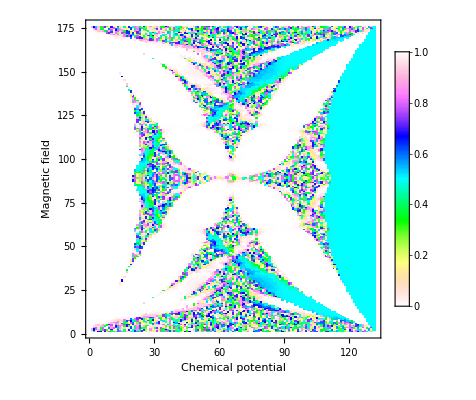

```mathematica
CoolColor[ z_ ] :=Hue[z,If[z<0.5,3z,3-3z],1];
(*only fractional part matters*)
fracC=Mod[νculC,1];

ListDensityPlot[fracC, ColorFunction ->CoolColor,PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
```

### Extra